#### Resultats de calculations sur une structure de Si relaxed

```mathematica
NotebookDirectory[]
```

/home/sebastien/Documents/DFTU/matteo/

```mathematica
resultsecut={#[[1]], #[[-1]]}&/@Rest@Import[NotebookDirectory[]<> "res-ecut.dat"];
resultsecut=Rest@Import[NotebookDirectory[]<> "res-ecut.dat"];
resultscut=Rest@Import[NotebookDirectory[]<> "res-cut.dat"];
```

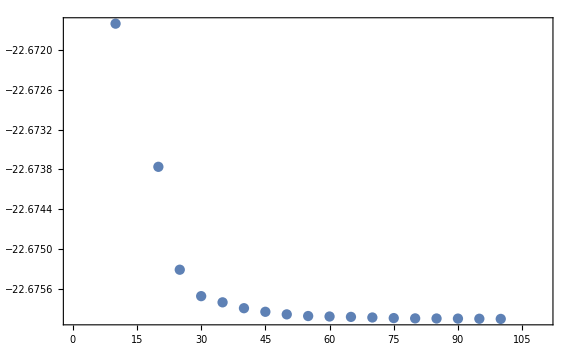

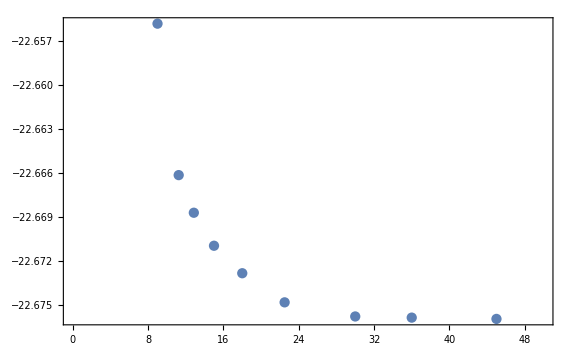

```mathematica
ListPlot[{#[[1]], #[[-1]]}&/@resultsecut, PlotRange->{{0, 110}, All }, ImageSize->Large, Frame->True]
ListPlot[{#[[1]], #[[-1]]}&/@resultscut, PlotRange->{{0, 50}, All }, ImageSize->Large, Frame->True]
```

```mathematica
results[[-1]];
```

Part::partd: Part specification results⟦-1⟧ is longer than depth of object.

Fait un threeshold automatically

```mathematica
(*Enleve les lattices parameter qui ne sert a rien, optionnel*)
(*results=Rest[#]&/@results;*)
(*Enleve les k parameter qui ne sert a rien, optionnel*)
(*results=Rest[#]&/@results*)
```

```mathematica
thr1=0.0005;
thr2=0.4;
```

```mathematica
resultsA=resultsecut;
```

#### Implementation de lecture automatique

```mathematica
returnFirstConverged[list_, eps_]:=Module[{ thr=eps/2,templist=list,  trend=0, l1, l2},
(*fonctionne*)
While[trend==0,
l1=Length@templist;
If[l1==1, Return[0]];


Do[
If[templist[[1]][[-1]]-thr>=templist[[i+1]][[-1]] || templist[[1]][[-1]]+thr<=templist[[i+1]][[-1]] ,
templist=Rest@templist, Break[]],

{i, 2,l1 }];

l2=Length@templist;
If[l2==1, Return[0]];
If[Length@l1==Length@l2, Return[templist[[1]]]];
]
]
```

#### Test Zone

```mathematica
Dynamic@returnFirstConverged[resultsA, thr1]
```

#### FIt parabole

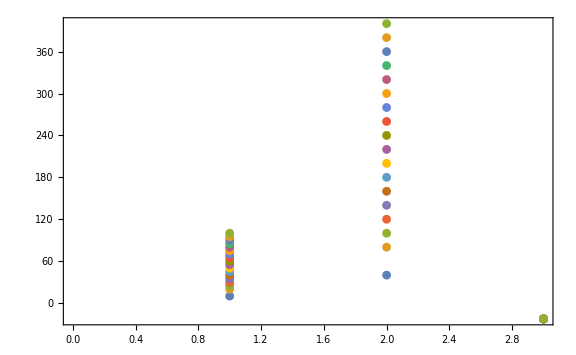

ListPlot::lpn: resultsAPressure is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[resultsAPressure,ImageSize→Large,Frame→True]

```mathematica
ListPlot[resultsA, ImageSize->Large, Frame->True]
ListPlot[resultsAPressure, ImageSize->Large, Frame->True]
```

```mathematica
fit=NonlinearModelFit[resultsA, a x^2+b x + c, {a, b, c}, x];
function=Normal[fit]
minPoint={a, b}/.{b->Minimize[function, x][[1]], a->x/.Minimize[function, x][[2]]}
```

NonlinearModelFit::fitc: Number of coordinates (2) is not equal to the number of variables (1).

General::stop: Further output of NonlinearModelFit::fitc will be suppressed during this calculation.

NonlinearModelFit[{{10.,40.,-22.6716},{20.,80.,-22.6738},{25.,100.,-22.6753},{30.,120.,-22.6757},{35.,140.,-22.6758},{40.,160.,-22.6759},{45.,180.,-22.6759},{50.,200.,-22.676},{55.,220.,-22.676},{60.,240.,-22.676},{65.,260.,-22.676},{70.,280.,-22.676},{75.,300.,-22.676},{80.,320.,-22.676},{85.,340.,-22.676},{90.,360.,-22.676},{95.,380.,-22.676},{100.,400.,-22.6761}},c+b x+a x^2,{a,b,c},x]

NonlinearModelFit::fitc: Number of coordinates (2) is not equal to the number of variables (1).

General::stop: Further output of NonlinearModelFit::fitc will be suppressed during this calculation.

General::ivar: -0.829053 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NMinimize::nnum: The function value NonlinearModelFit[{{10.,40.,-22.6716},{20.,80.,-22.6738},{25.,100.,-22.6753},{30.,120.,-22.6757},{35.,140.,-22.6758},{40.,160.,-22.6759},«6»,{75.,300.,-22.676},{80.,320.,-22.676},{85.,340.,-22.676},{90.,360.,-22.676},{95.,380.,-22.676},{100.,400.,-22.6761}},«2»,-«19»] is not a number at {x} = {-0.829053}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {b→NonlinearModelFit[{{10.,40.,-22.6716},{20.,80.,-22.6738},{25.,100.,-22.6753},{30.,120.,-22.6757},{35.,140.,-22.6758},{40.,160.,-22.6759},«7»,{80.,320.,-22.676},{85.,340.,-22.676},{90.,360.,-22.676},{95.,380.,-22.676},{100.,400.,-22.6761}},c+b x+a x^2,{a,b,c},x],a→x/.x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{a,b}/.{b→NonlinearModelFit[{{10.,40.,-22.6716},{20.,80.,-22.6738},{25.,100.,-22.6753},{30.,120.,-22.6757},{35.,140.,-22.6758},{40.,160.,-22.6759},{45.,180.,-22.6759},{50.,200.,-22.676},{55.,220.,-22.676},{60.,240.,-22.676},{65.,260.,-22.676},{70.,280.,-22.676},{75.,300.,-22.676},{80.,320.,-22.676},{85.,340.,-22.676},{90.,360.,-22.676},{95.,380.,-22.676},{100.,400.,-22.6761}},c+b x+a x^2,{a,b,c},x],a→x/.x}

```mathematica
Plot[fit[x],{x,10,10.6},Epilog:>Point[resultsA],PlotStyle->{Orange,Thick}, Frame->True, ImageSize->Large]
```

General::ivar: 10. is not a valid variable.

General::ivar: 10.0123 is not a valid variable.

General::ivar: 10.0245 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

#### Test Engauge

```mathematica
path="/home/bienvenue/Documents/DFPT+U/EX-Si/";
```